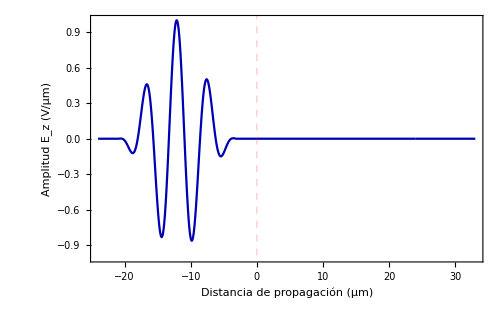

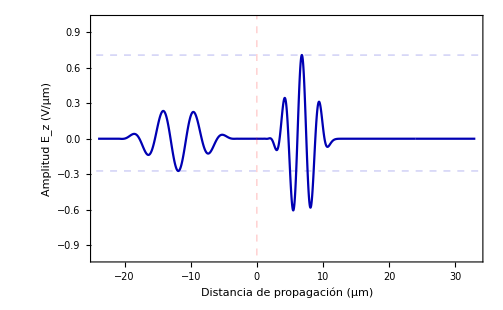

```mathematica
SetDirectory [NotebookDirectory[]];
deltatime=Import["Enodos1.txt",{"Data",1,1}]*10^-15; (*s*)
c=3*10^8; (*m/s*)
deltaSpace=deltatime*c;
size=Import["Enodos1.txt",{"Data",2,1}];
wall=Import["Enodos1.txt",{"Data",3,1}];
posdiscontinuidad=0;

campoEnodos1=Import["Enodos1.txt",{"Data",Range[4,size+3],2}];
datosEnodos1=Table[{(-wall+i)*deltaSpace*10^6,campoEnodos1[[i]]},{i,1,size}];
puntosEt2=ListPlot[datosEnodos1,PlotStyle-> {PointSize[0.01],RGBColor[0,0,0.7]},PlotRange->{All,{-1,1}},Joined->True,Frame->True, FrameLabel->{"Distancia de propagación (μm)","Amplitud E_z (V/μm)"},FrameStyle->{Directive[Black,16],Directive[Black,16]},GridLines->{{{posdiscontinuidad,Directive[RGBColor[1,0,0],Dashed,Thick]}},None}, AxesOrigin->{100,0}]

campoEnodos2=Import["Enodos2.txt",{"Data",Range[4,size+3],2}];
datosEnodos2=Table[{(-wall+i)*deltaSpace*10^6,campoEnodos2[[i]]},{i,1,size}];
ListPlot[datosEnodos2,PlotStyle-> {PointSize[0.01],RGBColor[0,0,0.7]},PlotRange->{All,{-1,1}},Joined->True,Frame->True, FrameLabel->{"Distancia de propagación (μm)","Amplitud E_z (V/μm)"},FrameStyle->{Directive[Black,16],Directive[Black,16]},GridLines->{{{posdiscontinuidad,Directive[RGBColor[1,0,0],Dashed,Thick]}},{{0.7063,Directive[RGBColor[0,0,0.8],Dashed,Thick]},{-0.2722,Directive[RGBColor[0,0,0.8],Dashed,Thick]}}}, AxesOrigin->{100,0}]
```

```mathematica
w=0.4;
f1z=0.39; (*Hz/fs*)
delta1z=0.1*f1z; (*Hz/fs*) (*Constante de amortiguamiento*)
w1z=2*Pi*f1z/w; (*rad/fs*) (*Frecuencia de Resonancia*)
εsz=3;
εinfz=1;
G1z=1;
b1z=G1z*(εsz-εinfz);
εrz[w_]:=εinfz+((εsz-εinfz)*w1z^2)/(w1z^2-2*I*w*delta1z-w^2);
Re[Sqrt[εrz[w]]]
Im[Sqrt[εrz[w]]]
```

1.73452

0.000483411